# Homework 5 Andrew Brown and Brian Carlson 3-7-14

## Problem 1. Police Robber Simulation

### Task

(i) Write a function checkinside [police1, police2, police3,robber] that given four points (by coordinates) returns true of the robber is inside the triangle formed by the police officers and false otherwise. (If the robber is on the boundary of the triangle, the function should return false.) 

(ii) Create a function easyRunaway [police1, police2, police3,robber, length , numberSteps].  Here the first four entries tell you the position of the robber and the police officers. length is the length of an individual step and numberSteps is the number of steps. Furthermore assume that the function checkinside [police1, police2, police3, robber] returns False, that is the function easyRunaway is only called if the robber is not inside the triangle formed by the police officers. 

(iii) Create a function cleverRunaway[police1, police2, police3,robber, length , numberSteps].  As before the first four entries tell you the position of the robber and the police officers. length is the length of an individual step and numberSteps is the number of steps. Furthermore assume that the function checkinside[police1, police2, police3,robber] returns True, that is the function cleverRunaway is only called if the robber is inside the triangle formed by the police officers. 

(iv) Using the parts (ii) and (iii) create Runaway [police1, police2, police3,robber,  length, numberSteps].  As before the first four entries tell you the position of the robber and the police officers. length is the length of an individual step and numberSteps is the number of steps. Now depending on where the robber current is s/he needs to follow strategy (ii) or (iii). Not that in the case the robber is on the triangle boundary the strategy of part (ii) is chosen. Call the functions developed in (ii) and (iii) in this function. Do not copy the code.

### Solution (i)

```mathematica
(*Check if robber is inside the triangle formed by the three policemen.*)
checkinside[police1_,police2_,police3_,robber_]:=Module[{sumOfAngles},
(*Sum the angles formed by the robber with each of the three policemen.*)
sumOfAngles=angle[police1,robber,police2]
+angle[police1,robber,police3]
+angle[police2,robber,police3];
(*If the angles sum to 2π, the robber is inside the triangle.*)
Return[Abs[sumOfAngles-2π]<10^-10]
]
```

#### Helper Function For Solution (i)

```mathematica
(*Find the angle between the two vectors created by three points.*)
angle[a_,b_,c_]:=N[VectorAngle[
{a[[1]]-b[[1]],a[[2]]-b[[2]]},
{c[[1]]-b[[1]],c[[2]]-b[[2]]}]
]
```

#### Test Cases For Solution (i)

```mathematica
p1={-10,10};
p2={-10,0};
p3={0,0};
r1={-5,3};
```

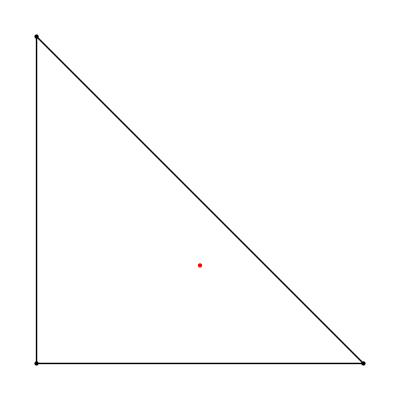

```mathematica
Graphics[{Black,Line[{{p1,p2},{p2,p3},{p1,p3}}],PointSize[Large],Point[{p1,p2,p3}],Red,Point[r1]}]
```

Here, we can plainly see that the robber is inside of the triangle, so the function should return true.

```mathematica
checkinside[{p1,p2,p3},r]
```

True

```mathematica
p4={2,4};
p5={7,8};
p6={2,10};
r2={4,5};
```

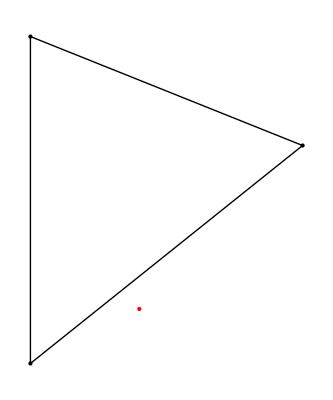

```mathematica
Graphics[{Black,Line[{{p4,p5},{p4,p6},{p5,p6}}],PointSize[Large],Point[{p4,p5,p6}],Red,Point[r2]}]
```

Here, we can plainly see that the robber is outside of the triangle, so the function should return false.

```mathematica
checkinside[{p4,p5,p6},r2]
```

False

```mathematica
p7={9,-4};
p8={5,-9};
p9={1,1};
r3={0,0};
```

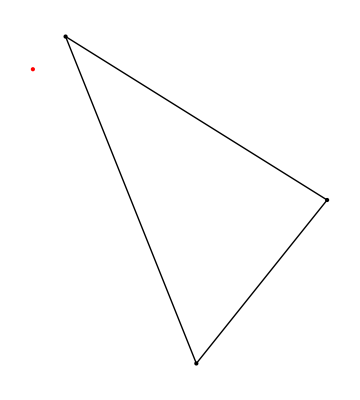

```mathematica
Graphics[{Black,Line[{{p7,p8},{p7,p9},{p8,p9}}],PointSize[Large],Point[{p7,p8,p9}],Red,Point[r3]}]
```

Here, we can plainly see that the robber is outside of the triangle, so the function should return false.

```mathematica
checkinside[{p7,p8,p9},r3]
```

False

### Solution (ii)

```mathematica
(*Simulates a robber running from outside of the triangle formed by three police, perpendicular to the nearest side of that triangle.*)
easyRunaway[police1_,police2_,police3_,robber_,length_,numberSteps_]:=Module[{closePoliceList = findTwoClosest[{police1,police2,police3},robber]},
(*Problem reduces to the 2-police case once the two nearest police have been found. Complement finds the one police that is not one of the closest.*)
robberRun[robber,closePoliceList[[1]],closePoliceList[[2]],Flatten[Complement[{police1,police2,police3},closePoliceList]],length,1,numberSteps]
]
```

#### Helper Functions for Solution (ii)

```mathematica
(*Finds the pair of policemen closest to the robber*)
findTwoClosest[policeList_,robber_]:=Module[{permutations={},distances={},position},
(*Take all permutations of 2 of the policemen.*)
permutations=DeleteDuplicates[Permutations[policeList,{2}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
(*Find the distances between the robber and the police for each permutation.*)
distances=(EuclideanDistance[#[[1]],robber]+EuclideanDistance[#[[2]]/2,robber])&/@permutations;
(*Find and return the minimum-distance permutation.*)
position=Flatten[Position[distances,Min[distances]]][[1]];
Return[permutations[[position]]]
]

(*Simulates the robber running perpendicular to the line formed by the two nearest policemen. Taken from code written in-class when the problem was introduced.*)
robberRun[robberco_,police1co_,police2co_,police3co_,speed_,timestep_,stepnum_]:= Module[{pol1x = police1co[[1]],pol1y = police1co[[2]],
pol2x = police2co[[1]], pol2y = police2co[[2]],pol3x = police3co[[1]],pol3y = police3co[[2]],currentRobx = robberco[[1]],currentRoby = robberco[[2]], i, L = speed * timestep,robberPt = {robberco},police1Pt={police1co},
police2Pt={police2co},police3Pt = {police3co},policeSlope, xchange, ychange,dx,dy},
(*The slope of the line formed by the police points.*)
policeSlope=(pol2y-pol1y)/(pol2x-pol1x);
(*Solve for the xchange and ychange, where they satisfy the Pythagorean identity in summing to the step length and are perpendicular to the police line.*)
{xchange,ychange} =Abs[{dx,dy}/.NSolve[{L^2 == dx^2+dy^2, dy/dx == -1/policeSlope}, {dx,dy}][[1]]];
(*Iterate stepnum times.*)
For[i = 1, i ≤ stepnum, i++, 
(*The new police coordinates are determined by multiplying the steplength by cosine and sine so that they move in the direction of the robber.*)
pol1x = pol1x+ L * (currentRobx - pol1x) / √((currentRobx - pol1x)^2 + (currentRoby - pol1y)^2);
pol1y = pol1y+ L * (currentRoby- pol1y) / √((currentRobx - pol1x)^2 + (currentRoby - pol1y)^2);
AppendTo[police1Pt, {pol1x, pol1y}];
pol2x= pol2x+ L * (currentRobx- pol2x) / √((currentRobx - pol2x)^2 + (currentRoby- pol2y)^2);
pol2y = pol2y+ L * (currentRoby - pol2y) / √((currentRobx- pol2x)^2 + (currentRoby- pol2y)^2);
AppendTo[police2Pt, {pol2x, pol2y}];
pol3x= pol3x+ L * (currentRobx- pol3x) / √((currentRobx - pol3x)^2 + (currentRoby- pol3y)^2);
pol3y = pol3y+ L * (currentRoby - pol3y) / √((currentRobx- pol3x)^2 + (currentRoby- pol3y)^2);
AppendTo[police3Pt, {pol3x, pol3y}];
(*Add or subtract the x- and ychange for the robber based on the position of the two police.*)
If[robberco[[2]] > (robberco[[1]]- Min[{police1co[[1]], police2co[[1]]}]) * policeSlope + Min[{police1co[[2]], police2co[[2]]}],
currentRoby = currentRoby + ychange,
currentRoby = currentRoby -ychange
];
If[robberco[[1]] > (robberco[[2]]- Min[{police1co[[2]], police2co[[2]]}]) / policeSlope+ Min[{police1co[[1]], police2co[[1]]}],
currentRobx = currentRobx + xchange, 
currentRobx = currentRobx - xchange
];
AppendTo[robberPt, {currentRobx, currentRoby}];
];
(*Return a plot of all of the points for the police and the robber.*)
Return[
Show[
ListPlot[{police1Pt,police2Pt,police3Pt,robberPt, {police1co, police2co,police3co}, {robberco}}, PlotStyle -> {{Blue, PointSize[Small]}, {Purple ,PointSize[Small]},{Yellow,PointSize[Small]}, {Red, PointSize[Small]},{Green, PointSize[Large]}, {Orange,PointSize[Large]},{Red, PointSize[Large]}}, Joined -> {True, True,True,True, False,False, False}]
]
]
]
```

#### Test Cases For Solution (ii)

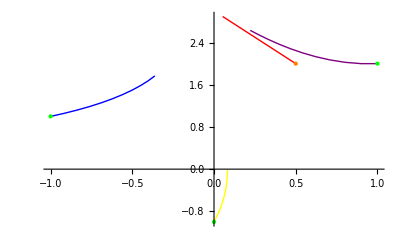

```mathematica
easyRunaway[{-1,1},{0,-1},{1,2},{0.5,2},.1,10]
```

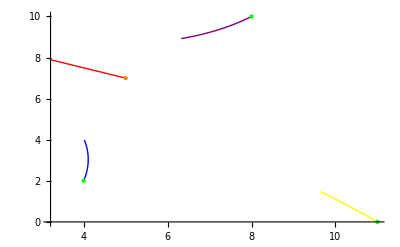

```mathematica
easyRunaway[{4,2},{8,10},{11,0},{5,7},.1,20]
```

We know that a right angle is at ((√2)/2,(√2)/2)

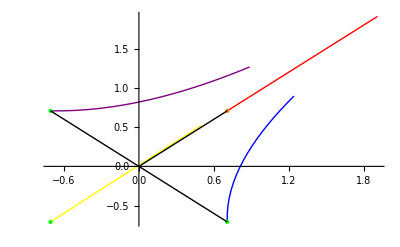

```mathematica
Show[easyRunaway[{(√2)/2,(-√2)/2},{(-√2)/2,(√2)/2},{(-√2)/2,(-√2)/2},{(√2)/2,(√2)/2},.1,17],Graphics[{Black,Line[{{(√2)/2,(-√2)/2},{(-√2)/2,(√2)/2}}],Line[{{0,0},{(√2)/2,(√2)/2}}]}]]
```

### Solution (iii)

```mathematica
(*Simulates a robber running away from police, starting inside the triangle that they determine. Once the robber reaches the nearest midpoint, he runs perpendicular to that side.*)
cleverRunaway[police1_,police2_,police3_,robber_,length_,numberSteps_]:=Module[{police1Pt = {police1},police2Pt = {police2},police3Pt = {police3},pol1x = police1[[1]],pol1y = police1[[2]],pol2x = police2[[1]],pol2y = police2[[2]],pol3x = police3[[1]],pol3y = police3[[2]],robberPt = {robber},robberCo = robber,closePoliceList = findNearestMidpoint[{police1,police2,police3},robber],i,xchange, ychange,dx, dy},
(*Solve for the xchange and ychange, where they satisfy the Pythagorean identity in summing to the step length and are perpendicular to the police line.*)
{xchange,ychange} =Abs[{dx,dy}/.NSolve[{length^2 == dx^2+dy^2, dy/dx == -1/(closePoliceList[[1,2]]-closePoliceList[[2,2]])/(closePoliceList[[1,1]]-closePoliceList[[2,1]])}, {dx,dy}][[1]]];
(*Iterate numberSteps times.*)
For[i = 1, i ≤ numberSteps, i++,
(*Determine if the robber is inside the triangle but not on the line.*)
If[checkinside[{pol1x,pol1y},{pol2x,pol2y},{pol3x,pol3y},robberCo]&&!liesOnLine[closePoliceList,robberCo],
(*If inside, take a step toward the nearest midpoint.*)
robberCo = returnRobberCoordInside[robberCo,closePoliceList,length],
(*Run in the direction that increases distance from the third policeman once outside or on the line of the triangle..*)
If[Abs[robberCo[[2]]+ychange - Flatten[Complement[{police1,police2,police3},closePoliceList]][[2]]]>Abs[robberCo[[2]] - Flatten[Complement[{police1,police2,police3},closePoliceList]][[2]]],
robberCo[[2]]= robberCo[[2]]+ ychange,
robberCo[[2]]= robberCo[[2]]- ychange
];
If[Abs[robberCo[[1]]+xchange - Flatten[Complement[{police1,police2,police3},closePoliceList]][[1]]]>Abs[robberCo[[1]] - Flatten[Complement[{police1,police2,police3},closePoliceList]][[1]]],
robberCo[[1]]= robberCo[[1]]+ xchange, 
robberCo[[1]]= robberCo[[1]]- xchange
];

];
AppendTo[robberPt,robberCo];
(*All of the police take a step toward the robber.*)
pol1x = pol1x+ length * (robberCo[[1]]- pol1x) / √((robberCo[[1]] - pol1x)^2 + (robberCo[[2]] - pol1y)^2 );
pol1y = pol1y+ length * (robberCo[[2]]- pol1y) / √((robberCo[[1]] - pol1x)^2 + (robberCo[[2]] - pol1y)^2 );
AppendTo[police1Pt, {pol1x, pol1y}];
pol2x= pol2x+ length* (robberCo[[1]]- pol2x) / √((robberCo[[1]]- pol2x)^2 + (robberCo[[2]]- pol2y)^2 );
pol2y = pol2y+ length * (robberCo[[2]] - pol2y) / √((robberCo[[1]]- pol2x)^2 + (robberCo[[2]]- pol2y)^2 );
AppendTo[police2Pt, {pol2x, pol2y}];
pol3x= pol3x+ length * (robberCo[[1]]- pol3x) / √((robberCo[[1]] - pol3x)^2 + (robberCo[[2]]- pol3y)^2 );
pol3y = pol3y+ length * (robberCo[[2]] - pol3y) / √((robberCo[[1]]- pol3x)^2 + (robberCo[[2]]- pol3y)^2 );
AppendTo[police3Pt, {pol3x, pol3y}];
];
(*Return a plot of all of the police and robber, along with their initial locations.*)
Return[
Show[
ListPlot[{police1Pt,police2Pt,police3Pt,robberPt, {police1, police2,police3}, {robber}}, PlotStyle -> {{Blue, PointSize[Small]}, {Purple ,PointSize[Small]},{Yellow,PointSize[Small]}, {Red, PointSize[Small]},{Green, PointSize[Large]}, {Orange,PointSize[Large]},{Red, PointSize[Large]}}, Joined -> {True, True,True,True, False,False, False}]
]
]
]
```

#### Helper Functions For Solution (iii)

```mathematica
(*Finds the new coordinates of the robber after one step toward the nearest midpoint.*)
returnRobberCoordInside[robber_,closePoliceList_,length_]:=Module[{midpoint=1/2(closePoliceList[[1]] + closePoliceList[[2]]),angle},
(*Find the angle to the nearest midpoint.*)
angle=VectorAngle[{1,0},{midpoint[[1]]-robber[[1]],midpoint[[2]]-robber[[2]]}];
(*Use sine and cosine to add the y and x components to the robber coordinate.*)
Return[{length*Cos[angle]+robber[[1]],length*Sin[angle]+robber[[2]]}]
]

(*Finds the pair of policemen that have the midpoint nearest to the robber.*)
findNearestMidpoint[policeList_,robber_]:=Module[{permutations={},distances={},position},
(*Take all permutations of 2 of the policemen.*)
permutations=DeleteDuplicates[Permutations[policeList,{2}],{#1[[1]],#1[[2]]}=={#2[[2]],#2[[1]]}&];
(*Find the distances between the robber and the midpoint.*)
distances=EuclideanDistance[(#[[1]]+#[[2]])/2,robber]&/@permutations;
(*Find and return the minimum-distance permutation.*)
position=Flatten[Position[distances,Min[distances]]][[1]];
Return[permutations[[position]]]
]

(*Determines if the robber is on the line formed by the two police.*)
liesOnLine[police_,robber_]:=Module[{equ = LinearModelFit[police,x,x]},
(*Returns whether or not the robber is on the point determined by the linear fit of the two police.*)
Return[Abs[equ[robber[[1]]]-robber[[2]]]<10^-3]
]
```

#### Test Cases For Solution (iii)

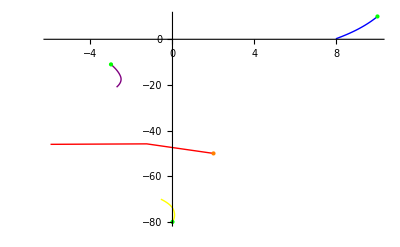

```mathematica
cleverRunaway[{10,10},{-3,-11},{0,-80},{2,-50},0.05,200]
```

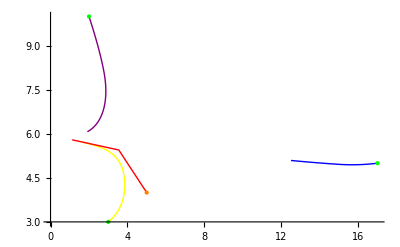

```mathematica
cleverRunaway[{17,5},{2,10},{3,3},{5,4},.05,90]
```

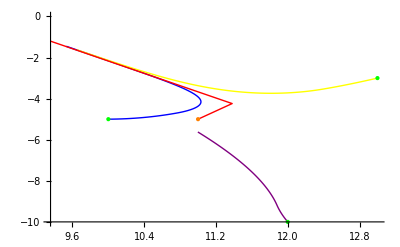

```mathematica
cleverRunaway[{10,-5},{12,-10},{13,-3},{11,-5},.05,90]
```

#### Limitations of Solution (iii)

There are a few instances when our program deviates from ideal behavior. We were not able to work out these bugs before the assignment was due. In the following examples, you can observe cases in which the movements of the robber act differently than expected.

1.) Sometimes, the transition from the inside to the outside of the triangle can display odd behaviors.

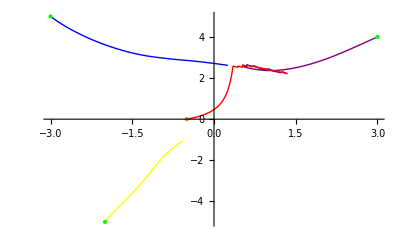

```mathematica
cleverRunaway[{-3,5},{3,4},{-2,-5},{-.5,0},.05,84]
```

2.) In our “NSolve” for finding the changes in x and y that corresponds to the step length, a “divide by zero” error occurs along with other problems.

Power::infy: Infinite expression 1/0 encountered.

NSolve::infc: The system 0.0025 == dx$2348226^2 + dy$2348226^2 && dy$2348226/dx$2348226 == ComplexInfinity contains an infinite object ComplexInfinity.

ReplaceAll::reps: {0.0025 == dx$2348226^2 + dy$2348226^2, dy$2348226/dx$2348226 == ComplexInfinity} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {xchange$2348226, ychange$2348226} and Abs[{dx$2348226, dy$2348226}/. {0.0025 == dx$2348226^2 + dy$2348226^2, dy$2348226/dx$2348226 == ComplexInfinity}] are not the same shape.

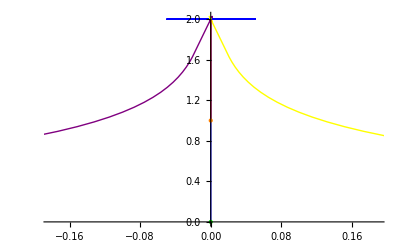

```mathematica
cleverRunaway[{0,0},{-1,0},{1,0},{0,1},.05,50]
```

3.) It would appear that if any two x or y coordinates are the same, a “divide by zero” error occurs.

Power::infy: Infinite expression 1/0 encountered.

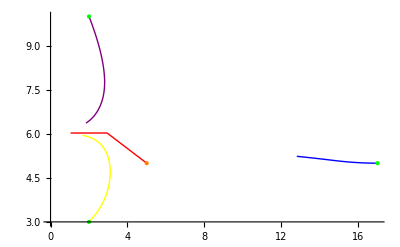

```mathematica
cleverRunaway[{17,5},{2,10},{2,3},{5,5},.05,84]
```

4.) It would appear as if the algorithm for finding the line perpendicular to the two nearest police officers tends to favor a counter-clockwise path. In this case, the robber doesn’t move towards the midpoint either.

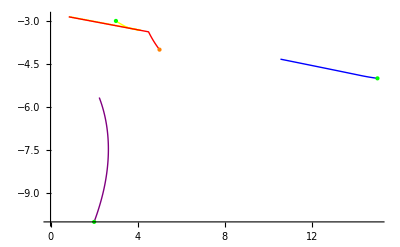

```mathematica
cleverRunaway[{15,-5},{2,-10},{3,-3},{5,-4},.05,90]
```

### Solution (iv)

```mathematica
(*Simulate a generalized robber running from three policemen, including if the robber is inside or outside of the triangle.*)
Runaway[police1_,police2_,police3_,robber_,length_,numberSteps_]:=Module[{},
(*If the robber is inside of the triangle, invoke cleverRunaway. Otherwise, invoke easyRunaway.*)
If[checkinside[police1,police2,police3,robber],
cleverRunaway[police1,police2,police3,robber,length,numberSteps],
easyRunaway[police1,police2,police3,robber,length,numberSteps]
]
]
```

#### Test Cases For Solution (iv)

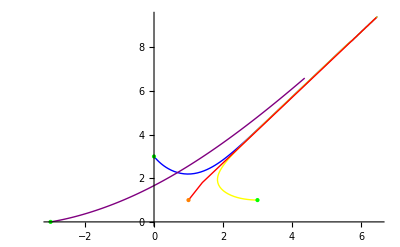

```mathematica
Runaway[{0,3},{-3,0},{3,1},{1,1},0.1,100]
```

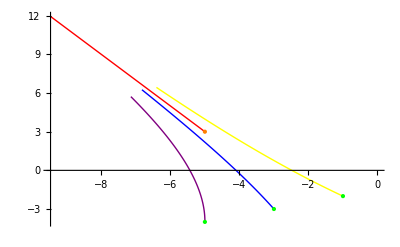

```mathematica
Runaway[{-3,-3},{-1,-2},{-5,-4},{-5,3},0.1,100]
```

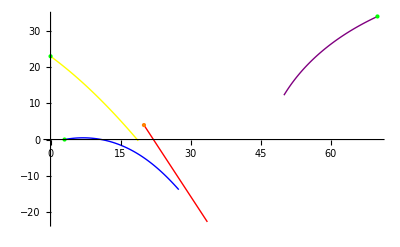

```mathematica
Runaway[{0,23},{3,0},{70,34},{20,4},0.1,300]
```

#### Limitations of Solution (iv)

Since “Solution (iv)” draws on the same code as “Solution (iii)”, the same limitations are present and can be demonstrated with the same examples.

## Problem 2. Sudoku Tester

### Task

(i) Write a function eachAtMostOnce[lst] which is given a list 4 entries. The function returns True if the list contains exactly four elements and contains each of the numbers from 1 to 4 at most once; the function returns False otherwise.  Do NOT assume that the list only contains numbers.

(ii) Write a function consistentPuzzle [entries] which is given a 4x4 set of Sudoku entries (using the format described above) and which returns True if the given 4x4 set of Sudoku entries is a valid Sudoku puzzle (that is each digit appears in each row, in each column, and in each block at most once); otherwise the function returns False. 

(iii) Write a function correctPuzzle [solution, entries ] which is given a 4x4 solution and a 4x4 set of Sudoku entries (both using the format described above). Assume the solution is a valid 4x4 set of Sudoku entries which contains no blanks. (That is a digit is specified for each square.) The function returns two list. The first list contains the locations of the squares where the a square with a digit in the 4x4 set of entries is incorrect. The second list contains the locations of the squares which contain no digit. If a puzzle is completely and correctly solved, both lists are empty. 

(iv) Write a function fillPuzzleSlot [entries, row, col] which is given a 4x4 set of Sudoku entries and a row and a column. The function attempts to determine the set of possible digits which may be placed at the given square - as specified by the row and column. The function returns a pair {exists , valueLst}. Exists is True, if the given square in the entries is already a digit. Otherwise it is False. valueLst is the list of values possible at that location based solely on checking the row, col, and block the given square is in. That is fillPuzzleSlot returns the list of digits which are not in the same row or in the same column, or in the same block.

### Lists For Testing

```mathematica
sudokuFilled={{2,1,3,4},{4,3,1,2},{3,2,4,1},{1,4,2,3}};

sudokuPartialWith10={{" ",1," ",4},{4," " ,1," "},{3," "," ",1},{1,4,2," "}};

sudokuPartialWith12={{3,1," ",4},{4,2 ,1," "},{2,3," ",1},{1,4,2," "}};

sudokuPartialWith7={{" ",1," "," "},{4," " ,1," "},{" ",2," ",1},{1," ",2," "}};

incorrectSudokuPartial={{1,2,3,4},{Null,Null,2,2},{2,1,3,Null},{3,Null,2,Null}};

with7=Grid[sudokuPartialWith7,
ItemSize->{2,2},Dividers -> {{{Thickness[4],True}},{{Thickness[4],True}}},
Background -> {Automatic,Automatic}];

with10=Grid[sudokuPartialWith10,
ItemSize->{2,2},Dividers -> {{{Thickness[4],True}},{{Thickness[4],True}}},
Background -> {Automatic,Automatic}];

with12=Grid[sudokuPartialWith12,
ItemSize->{2,2},Dividers -> {{{Thickness[4],True}},{{Thickness[4],True}}},
Background -> {Automatic,Automatic}];

filled=Grid[sudokuFilled,
ItemSize->{2,2},Dividers -> {{{Thickness[4],True}},{{Thickness[4],True}}},
Background -> {Automatic,Automatic}];
```

### Solution (i)

```mathematica
(*Determines if a list contains four elements, including each of the digits from 1 to 4 at most once a piece.*)
eachAtMostOnce[lst_]:=Module[{numLst = {1,2,3,4}, current,i},
(*Ensures that the length is 4*)
If[Length[lst]≠ 4, 
Return[False]];
(*Run through each of the elements.*)
For[i = 1, i ≤ Length[lst], i++,
(*If the element is a number in numLst, delete it from numLst.*)
current = lst[[i]];
(*Numbers greater than 4 or less than 1 are allowed and ignored.*)
If[IntegerQ[current]&&1≤current≤4,
(*If the number has already appeared, current will not be in numLst.*)
If[MemberQ[numLst,current], 
numLst = Delete[numLst, current];
numLst = Insert[numLst, "checked", current],
Return[False]
]
]
];
(*If all tests are passed, return true.*)
Return[True]
]
```

#### Test Cases For Solution (i)

```mathematica
eachAtMostOnce[{1,2,someVar,3}]
```

True

```mathematica
eachAtMostOnce[{1,1,,4}]
```

False

```mathematica
eachAtMostOnce[{4,1,,2}]
```

True

### Solution (ii)

```mathematica
(*Checks that a given  4 x 4 matrix is legal under the rules of Sudoku by looking only all of the rows, column, and blocks.*)
consistentPuzzle[entries_]:= Module[{checkList={},i},
(*For all four blocks, columns, and rows.*)
For[i = 1, i ≤ 4, i++,
(*Check that 1 through 4 appear each at most one time in each of the rows, columns, and blocks.*)
AppendTo[checkList, eachAtMostOnce[getBlock[entries],i]];
AppendTo[checkList, eachAtMostOnce[getColumn[entries],i]];
AppendTo[checkList, eachAtMostOnce[entries[[i]],i]];
];
(*If there were any false returns, the configuration is inconsistent with the rules.*)
Return[!MemberQ[checkList,False]]
]
```

#### Helper Functions For Solution (ii)

```mathematica
(*Gets a column of a 4 x 4 matrix.*)
getColumn[entries_,col_]:=Module[{colList = {},j},
(*Takes the col element in each of the rows of the matrix and appends to colList*)
For[j = 1, j ≤ Length[entries], j++,
AppendTo[colList, entries[[j]][[col]]]
];
Return[colList]
]
```

```mathematica
(*Gets a 2 x 2 block from a 4 x 4 Sudoku configuration.*)
getBlock[entries_,blockNo_]:=Module[{block = {}},
(*There is a simple function to generate the correct elements in the first and second blocks, but no such function was found for 3 or 4.*)
If[blockNo == 1||blockNo == 2,
AppendTo[block, entries[[1]][[2 * blockNo - 1]]];
AppendTo[block, entries[[1]][[2 * blockNo ]]];
AppendTo[block, entries[[2]][[2 * blockNo - 1]]];
AppendTo[block, entries[[2]][[2 * blockNo ]]];
Return[block]
];
If[blockNo == 3,
AppendTo[block,entries[[3]][[1]]];
AppendTo[block,entries[[3]][[2]]];
AppendTo[block,entries[[4]][[1]]];
AppendTo[block,entries[[4]][[2]]],
AppendTo[block,entries[[3]][[3]]];
AppendTo[block,entries[[3]][[4]]];
AppendTo[block,entries[[4]][[3]]];
AppendTo[block,entries[[4]][[4]]]
];
Return[block]
]
```

#### Test Cases For Solution (ii)

```mathematica
Grid[sudokuPartialWith10,Frame->All]
```

| 1 |   | 4
4 |   | 1 |  
3 |   |   | 1
1 | 4 | 2 |

We can see that there are no overlaps or numbers in the rows or columns, so our function should return true.

```mathematica
consistentPuzzle[sudokuPartialWith10]
```

True

```mathematica
Grid[incorrectSudokuPartial,Frame->All]
```

1 | 2 | 3 | 4
 |  | 2 | 2
2 | 1 | 3 | 
3 |  | 2 |

We can see that there is an or numbers in the rows or columns, so our function should return true.

```mathematica
consistentPuzzle[sudokuPartialWith12]
```

True

```mathematica
Grid[sudokuPartialWith7,Frame->All]
```

| 1 |   |  
4 |   | 1 |  
  | 2 |   | 1
1 |   | 2 |

We can see that there are no overlaps or numbers in the rows or columns, so our function should return true.

```mathematica
consistentPuzzle[sudokuPartialWith7]
```

True

### Solution (iii)

```mathematica
(*Compares a solution and attempt 4 x 4 configuration to determine where they differ. Returns the list of cells in which the attempt is incorrect and the list of cells the attempt has blank.*)
correctPuzzle[solution_,entries_]:=Module[{row,column,wrongLst = {},emptyLst = {}},
(*Looking at every row.*)
For[row = 1, row≤ 4, row++,
(*Looking at every column in each row.*)
For[column = 1, column ≤ 4, column++,
(*Anywhere the two are different and entries is not empty at that cell, append to wrongLst.*)
If[entries[[row]][[column]] ≠ solution[[row]][[column]] &&
entries[[row]][[column]] ≠ " ",
AppendTo[wrongLst, {row,column}]
];
(*If entries has an empty cell there, append to emptyLst.*)
If[entries[[row]][[column]] == " ",
AppendTo[emptyLst, {row,column}]]
]
];
(*Return the wrongLst and emptyLst.*)
Return[{wrongLst,emptyLst}]
]
```

#### Test Cases For Solution (iii)

```mathematica
correctPuzzle[sudokuFilled,sudokuPartialWith12]
filled
with12
```

{{{1,1},{2,2},{3,1},{3,2}},{{1,3},{2,4},{3,3},{4,4}}}

2 | 1 | 3 | 4
4 | 3 | 1 | 2
3 | 2 | 4 | 1
1 | 4 | 2 | 3

3 | 1 |   | 4
4 | 2 | 1 |  
2 | 3 |   | 1
1 | 4 | 2 |

```mathematica
correctPuzzle[sudokuFilled,sudokuPartialWith7]
filled
with7
```

{{{3,2}},{{1,1},{1,3},{1,4},{2,2},{2,4},{3,1},{3,3},{4,2},{4,4}}}

2 | 1 | 3 | 4
4 | 3 | 1 | 2
3 | 2 | 4 | 1
1 | 4 | 2 | 3

| 1 |   |  
4 |   | 1 |  
  | 2 |   | 1
1 |   | 2 |

```mathematica
correctPuzzle[sudokuFilled,sudokuPartialWith10]
filled
with10
```

{{},{{1,1},{1,3},{2,2},{2,4},{3,2},{3,3},{4,4}}}

2 | 1 | 3 | 4
4 | 3 | 1 | 2
3 | 2 | 4 | 1
1 | 4 | 2 | 3

| 1 |   | 4
4 |   | 1 |  
3 |   |   | 1
1 | 4 | 2 |

### Solution (iv)

```mathematica
(*Finds and returns all digits that could be placed in a particular cell. Determines if that cell is currently empty.*)
fillPuzzleSlot[entries_,row_,col_]:=Module[{block ,column,blockPoss = {},colPoss = {},numList = {1,2,3,4},rowPoss = {},blockNum = 1,i,manip = entries,
exists = NumberQ[entries[[row]][[col]]]},
(*Ensures that the current digit is not returned if that digit is illegally placed.*)
manip[[row]][[col]] = " ";
(*Determine which block the cell is in.*)
If[row > 2, blockNum++];
If[col > 2, blockNum++];
If[col > 2 && row > 2, blockNum++];
(*For all of the digits from 1 to 4, if that digit is not in the row, block, or column, it is possibly legal to place it in that cell.*)
For[i = 1, i ≤ 4, i++,
If[!MemberQ[getBlock[manip,blockNum],i],AppendTo[blockPoss,i]];
If[!MemberQ[getColumn[manip,col],i],AppendTo[colPoss,i]];
If[!MemberQ[manip[[row]],i],AppendTo[rowPoss,i]]
];
(*Return whether or not there is already a digit and the intersection of all possibly legal digits.*)
Return[{exists,Intersection[blockPoss,colPoss,rowPoss]}]
]
```

#### Test Cases For Solution (iv)

```mathematica
fillPuzzleSlot[sudokuPartialWith10,1,4]
with10
```

{True,{2,3,4}}

| 1 |   | 4
4 |   | 1 |  
3 |   |   | 1
1 | 4 | 2 |

```mathematica
fillPuzzleSlot[sudokuPartialWith12,4,4]
with12
```

{False,{3}}

3 | 1 |   | 4
4 | 2 | 1 |  
2 | 3 |   | 1
1 | 4 | 2 |

```mathematica
fillPuzzleSlot[sudokuPartialWith7,3,2]
with7
```

{False,{2,3,4}}

| 1 |   |  
4 |   | 1 |  
  | 2 |   | 1
1 |   | 2 |